```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<"HeterogeneousTemplate.wl";

GenerateMarkovTemplates[  MarkovProc_, NumTemplates_, LenTemplates_ ] :=
	(RandomFunction[MarkovProc,{#,LenTemplates}][[2]][[1]][[1]])&/@ConstantArray[1,NumTemplates];

RandomMarkovError[  Alphabet_,ProbVec_, LenTemplates_ ,gpo_,EnergyMatrix_,KineticMatrix_ ] :=  Module[ {inputtemplate,ErrorProbs},
	inputtemplate = RandomChoice[ ProbVec->Range[Alphabet],LenTemplates];
	ErrorProbs=(GetErrorProb[GetTransferMatrixList[gpo,
		EnergyMatrix,KineticMatrix,inputtemplate],inputtemplate]);
	Return[ErrorProbs];
 ]
```

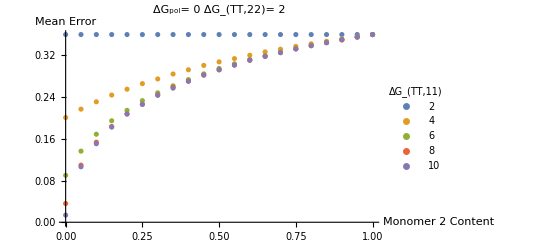

```mathematica
KineticMatrix =  {{0,0},{0,0}};
gpo = 0.0;

PreDomain =  Range[0,1,0.05];
ErrorData= {};
Domain = {1-#,#} &/@PreDomain;

For [ x = 2.0,x<=10.1,x = x+2.0,
	EnergyMatrix =  {{x,0},{0,2.0}};
	MeanErrors =RandomMarkovError[  2,#,100000,gpo,EnergyMatrix,KineticMatrix] &/@Domain;
	ErrorData =Append[ErrorData,Transpose@{PreDomain,MeanErrors}];
]

mu={2,4,6,8,10};
pl=PointLegend[mu,LegendLabel->Subscript["ΔG","TT,11"],LegendFunction->"Frame",LegendLayout->Automatic,LegendMarkers->Automatic];
p1 =ListPlot[ErrorData,AxesLabel->{"Monomer 2 Content","Mean Error"},
		PlotLegends->Placed[pl,Right],PlotLabel->Row[{Subscript["ΔG","pol"],"= 0    ",
		Subscript["ΔG","TT,22"],"= 2"}]]
```

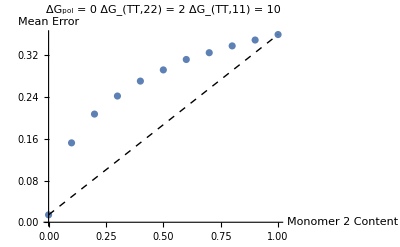

```mathematica
p1 =ListPlot[ErrorData[[6]],AxesLabel->{"Monomer 2 Content","Mean Error"}, 
	PlotLabel->Row[{Subscript["ΔG","pol"]," = 0    ",Subscript["ΔG","TT,22"],
	" = 2    ", Subscript["ΔG","TT,11"], " = 10 "}]];
p2 = Graphics[{Thick,Dashed,Line[{ErrorData[[6]][[1]],ErrorData[[6]][[-1]]}]}];
Show[{p1,p2}]
```

0.1

{1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1}

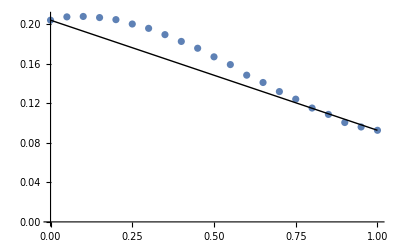

```mathematica
PreDomain[[3]]
RandomChoice[ {1-PreDomain[[3]],PreDomain[[3]]}->Range[2],100]
```

```mathematica
Save["ThermoCorrect.Error",ErrorData]
```